# Finite Rod, Albedo Problem, Isotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2016 Eugene d’Eon 
www.eugenedeon.com

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
a - length of the rod
-Graphics-

## Analytic solutions

### Reflectance/Transmittance

```mathematica
finrodalbedoiso`R[a_,α_,Σt_]:=α/(2 √(1-α)Coth[Σt a √(1-α)]-α+2)
```

```mathematica
finrodalbedoiso`T[a_,α_,Σt_]:=(2 √(1-α))/(2 √(1-α)Cosh[Σt a √(1-α)]-(α-2)Sinh[Σt a √(1-α)])
```

```mathematica
finrodalbedoiso`R[a_,α_,Σt_,n_]:=α^n(SeriesCoefficient[finrodalbedoiso`R[a,A,Σt],{A,0,n}]/.A->α);
finrodalbedoiso`T[a_,α_,Σt_,n_]:=α^n(SeriesCoefficient[finrodalbedoiso`T[a,A,Σt],{A,0,n}]/.A->α)
```

### ‘Radiance’

```mathematica
finrodalbedoiso`LR[x_,α_,Σt_,a_]:=(2 (-1+α) Cosh[(a-x) √(1-α) Σt]+√(1-α) (-2+α) Sinh[(a-x) √(1-α) Σt])/(2 (-1+α) Cosh[a √(1-α) Σt]+√(1-α) (-2+α) Sinh[a √(1-α) Σt])
```

```mathematica
finrodalbedoiso`LL[x_,α_,Σt_,a_]:=-(√(1-α) α Sinh[(a-x) √(1-α) Σt])/(2 (-1+α) Cosh[a √(1-α) Σt]+√(1-α) (-2+α) Sinh[a √(1-α) Σt])
```

### Fluence

```mathematica
finrodalbedoiso`ϕ[x_,α_,Σt_,a_]:=finrodalbedoiso`LR[x,α,Σt,a]+finrodalbedoiso`LL[x,α,Σt,a]
```

## Monte Carlo comparisons

```mathematica
finrodalbedoiso`ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
finrodalbedoiso`fs=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_isotropicscatter_exp_c0.7_mut1_*"];
```

### Reflectance/Transmittance

```mathematica
finrodalbedoiso`MCR[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[3,4]]}
];
finrodalbedoiso`MCT[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[4,4]]}
]
```

```mathematica
finrodalbedoiso`Rs=Table[finrodalbedoiso`MCR[f],{f,finrodalbedoiso`fs}];
finrodalbedoiso`Ts=Table[finrodalbedoiso`MCT[f],{f,finrodalbedoiso`fs}];
```

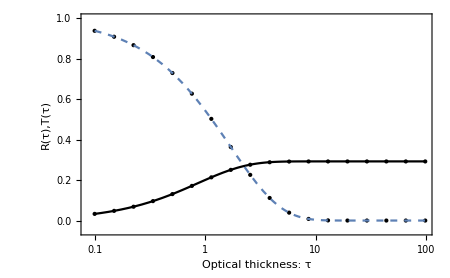

```mathematica
vizfiniterodRTiso=Show[
ListLogLinearPlot[finrodalbedoiso`Rs,PlotRange->{-0.05,1},PlotStyle->{PointSize[Medium],Black}],
ListLogLinearPlot[finrodalbedoiso`Ts,PlotRange->{-0.05,1},PlotStyle->{PointSize[Medium],Black}],
LogLinearPlot[finrodalbedoiso`R[a,0.7,1],{a,0.1,100},PlotStyle->Black],
LogLinearPlot[finrodalbedoiso`T[a,0.7,1],{a,0.1,100},PlotStyle->Dashed],
ImageSize->450,
Frame->True,FrameLabel->{{"R(τ),T(τ)",},{"Optical thickness: τ","Total Reflectance/Transmittance (R/T): isotropically-scattering finite rod"}}
]
```

```mathematica
finrodalbedoiso`fs2=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_isotropicscatter_exp_*length2.6*"];
```

```mathematica
finrodalbedoiso`MCR2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[3,4]]}
];
finrodalbedoiso`MCT2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[4,4]]}
]
```

```mathematica
finrodalbedoiso`Rs2=Table[finrodalbedoiso`MCR2[f],{f,finrodalbedoiso`fs2}];
finrodalbedoiso`Ts2=Table[finrodalbedoiso`MCT2[f],{f,finrodalbedoiso`fs2}];
```

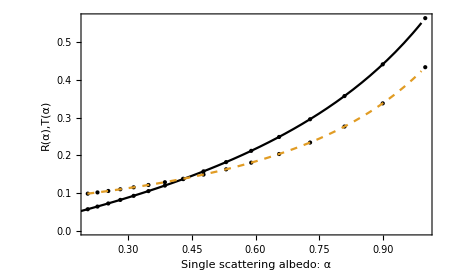

```mathematica
finiterodvarycplot=Show[
ListPlot[finrodalbedoiso`Rs2,PlotStyle->{PointSize[Medium],Black}],
ListPlot[finrodalbedoiso`Ts2,PlotStyle->{PointSize[Medium],Black}],
Plot[{finrodalbedoiso`R[2.6,c,1],finrodalbedoiso`T[2.6,c,1]},{c,0.01,.99},PlotRange->{0,.7},PlotStyle->{Black,Dashed}],
ImageSize->450,
Frame->True,FrameLabel->{{"R(α),T(α)",},{"Single scattering albedo: α","Total Reflectance/Transmittance (R/T): isotropically-scattering finite rod"}}
]
```

### Select simulation

```mathematica
finrodalbedoiso`fs=FileNames["code/rod/finiterod/albedoProblem/data/finiterod_albedoproblem_isotropicscatter_exp_c0.7_mut0.8*"];
finrodalbedoiso`filename=finrodalbedoiso`fs[[1]];
finrodalbedoiso`data=Import[finrodalbedoiso`filename,"Table"];
finrodalbedoiso`Σt=finrodalbedoiso`data[[1,11]];
finrodalbedoiso`α=finrodalbedoiso`data[[2,3]];
finrodalbedoiso`a=finrodalbedoiso`data[[2,5]];
finrodalbedoiso`dx=finrodalbedoiso`data[[2,7]];
finrodalbedoiso`numcollorders=finrodalbedoiso`data[[2,11]];
finrodalbedoiso`nummoments=finrodalbedoiso`data[[2,13]];
finrodalbedoiso`g=finrodalbedoiso`data[[1,-1]];
finrodalbedoiso`densmom=finrodalbedoiso`data[[11]];
```

### Internal Distributions

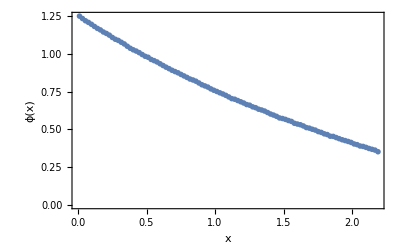

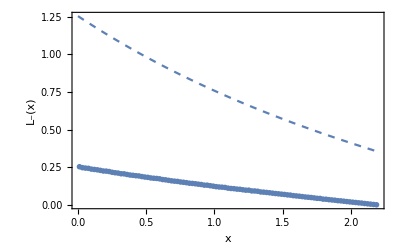

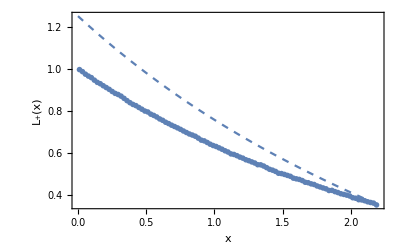

```mathematica
finrodalbedoiso`pointsCL = finrodalbedoiso`data[[10]];
(* divide by Σt to convert collision density into L *)
finrodalbedoiso`plotpointsCL=finrodalbedoiso`ppoints[finrodalbedoiso`pointsCL,finrodalbedoiso`dx,finrodalbedoiso`a,finrodalbedoiso`Σt];
finrodalbedoiso`pointsCR = finrodalbedoiso`data[[12]];
finrodalbedoiso`plotpointsCR=finrodalbedoiso`ppoints[finrodalbedoiso`pointsCR,finrodalbedoiso`dx,finrodalbedoiso`a,finrodalbedoiso`Σt];
(* divide by Σt to convert collision density into fluence *)
finrodalbedoiso`plotpointsϕ=finrodalbedoiso`ppoints[finrodalbedoiso`pointsCL+finrodalbedoiso`pointsCR,finrodalbedoiso`dx,finrodalbedoiso`maxx,finrodalbedoiso`Σt];

finrodalbedoiso`plotϕ=Show[
ListPlot[finrodalbedoiso`plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finrodalbedoiso`ϕ[x,finrodalbedoiso`α,finrodalbedoiso`Σt,finrodalbedoiso`a],{x,0,finrodalbedoiso`a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Finite rod, albedo problem, isotropic scattering, fluence ϕ[x], α = "<>ToString[finrodalbedoiso`α]<>", Σ_t = "<>ToString[finrodalbedoiso`Σt]<>", a = "<>ToString[finrodalbedoiso`a]}}
]

finrodalbedoiso`plotLL=Show[
ListPlot[finrodalbedoiso`plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finrodalbedoiso`LL[x,finrodalbedoiso`α,finrodalbedoiso`Σt,finrodalbedoiso`a],{x,0,finrodalbedoiso`a},PlotRange->All],
Plot[finrodalbedoiso`ϕ[x,finrodalbedoiso`α,finrodalbedoiso`Σt,finrodalbedoiso`a],{x,0,finrodalbedoiso`a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Finite rod, albedo problem, isotropic scattering, L_-[x], α = "<>ToString[finrodalbedoiso`α]<>", Σ_t = "<>ToString[finrodalbedoiso`Σt]<>", a = "<>ToString[finrodalbedoiso`a]}},PlotRange->All
]

finrodalbedoiso`plotLR=Show[
ListPlot[finrodalbedoiso`plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finrodalbedoiso`LR[x,finrodalbedoiso`α,finrodalbedoiso`Σt,finrodalbedoiso`a],{x,0,finrodalbedoiso`a},PlotRange->All],
Plot[finrodalbedoiso`ϕ[x,finrodalbedoiso`α,finrodalbedoiso`Σt,finrodalbedoiso`a],{x,0,finrodalbedoiso`a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Finite rod, albedo problem, isotropic scattering, L_+[x], α = "<>ToString[finrodalbedoiso`α]<>", Σ_t = "<>ToString[finrodalbedoiso`Σt]<>", a = "<>ToString[finrodalbedoiso`a]}},PlotRange->All
]
```

### Nth-scattered Reflectance

```mathematica
finrodalbedoiso`Rs=N[{finrodalbedoiso`data[[6]]}];
finrodalbedoiso`ns=Table[n,{n,0,finrodalbedoiso`numcollorders-1}];
finrodalbedoiso`analytic=Table[finrodalbedoiso`R[finrodalbedoiso`a,finrodalbedoiso`α,finrodalbedoiso`Σt,n],{n,finrodalbedoiso`ns}];
finrodalbedoiso`j=Join[{finrodalbedoiso`ns},{finrodalbedoiso`analytic},finrodalbedoiso`Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[finrodalbedoiso`j]]
]
```

n | analytic | MC
0 | 0. | 0.
1 | 0.16982 | 0.169702
2 | 0.0530554 | 0.0529898
3 | 0.0188762 | 0.0188996
4 | 0.00696225 | 0.0069549
5 | 0.00259536 | 0.0025943
6 | 0.00097059 | 0.0009506
7 | 0.000363326 | 0.0003673
8 | 0.000136046 | 0.0001358
9 | 0.0000509468 | 0.000049

### Nth-scattered Transmittance

```mathematica
finrodalbedoiso`Ts=N[{finrodalbedoiso`data[[8]]}];
finrodalbedoiso`ns=Table[n,{n,0,finrodalbedoiso`numcollorders-1}];
finrodalbedoiso`analytic=Table[finrodalbedoiso`T[finrodalbedoiso`a,finrodalbedoiso`α,finrodalbedoiso`Σt,n],{n,finrodalbedoiso`ns}];
finrodalbedoiso`j=Join[{finrodalbedoiso`ns},{finrodalbedoiso`analytic},finrodalbedoiso`Ts];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[finrodalbedoiso`j]]
]
```

n | analytic | MC
0 | 0.172045 | 0.172147
1 | 0.10598 | 0.10578
2 | 0.0460752 | 0.0460467
3 | 0.0180818 | 0.0179851
4 | 0.00687125 | 0.0068802
5 | 0.00258492 | 0.0025857
6 | 0.000969392 | 0.0009688
7 | 0.000363189 | 0.0003783
8 | 0.000136031 | 0.0001391
9 | 0.000050945 | 0.0000494

### Nth order fluence/density

```mathematica
finrodalbedoiso`nthϕ=finrodalbedoiso`data[[16+finrodalbedoiso`numcollorders+1;;16+2finrodalbedoiso`numcollorders]];
```

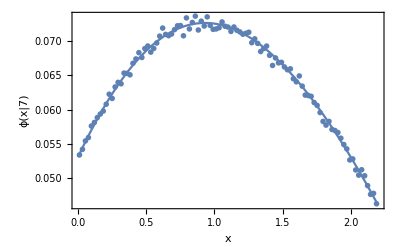

```mathematica
(* choose order:*)
finrodalbedoiso`n=2;

Clear[c,x];
finrodalbedoiso`phin=SeriesCoefficient[finrodalbedoiso`ϕ[x,c,finrodalbedoiso`Σt,finrodalbedoiso`a],{c,0,finrodalbedoiso`n}](finrodalbedoiso`α)^(finrodalbedoiso`n);
finrodalbedoiso`plotphin=Show[
ListPlot[finrodalbedoiso`ppoints[finrodalbedoiso`nthϕ[[finrodalbedoiso`n+2]],finrodalbedoiso`dx,finrodalbedoiso`a,finrodalbedoiso`Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[finrodalbedoiso`phin,{x,0,finrodalbedoiso`a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ["x|7"],},{x,"Semi-Infinite Rod, isotropic point, isotropic scattering, ϕ[x|"<>ToString[finrodalbedoiso`n]<>"], α = "<>ToString[finrodalbedoiso`α]<>", Σ_t = "<>ToString[finrodalbedoiso`Σt]}},PlotRange->All
]
```